# Coupled Analysis of Rocky

This notebook walks through the computation of the transfer function for a system that drives Rocky’s angle to 0 using PI control, while using PI control to control the motor.  One thing to notice in this notebook is that I am using the Mathematica function Factor to put the transfer function into the form of a polynomial over another polynomial.  Mathematica’s Simplify function tends to give you transfer functions that involve the ratio of two functions that are not polynomials.  I have found Factor to be a solution for this annoying issue.

The diagram below summarizes the whole system.  The diagram shows the nested structure of the block diagram.  To help connect the diagram to the computation of the transfer functions, all of the labels of the blocks correspond directly to the names of the variables below.  The transfer function for the motor was taken from night 4, and the transfer function relating velocity to angle was taken from the synthesis activity from day 5.

-Graphics-

```mathematica
Subscript[G, MOTOR]= β α /(s+α);
Subscript[G, MOTORCONTROLLER]=Subscript[J, p]+Subscript[J, i]/s;
Subscript[G, CONTROLLEDMOTOR] = Factor[Subscript[G, MOTOR] Subscript[G, MOTORCONTROLLER]/(1+Subscript[G, MOTOR] Subscript[G, MOTORCONTROLLER])];
Subscript[G, ANGLECONTROLLER]=Subscript[K, p]+Subscript[K, i]/s;
Subscript[G, VELOCITYTOANGLE]=-s/(L s^2- g);
Subscript[G, PLANT]=Factor[Subscript[G, CONTROLLEDMOTOR] Subscript[G, VELOCITYTOANGLE]];
Subscript[G, TOTALSYSTEM]=Factor[Subscript[G, ANGLECONTROLLER] Subscript[G, PLANT] / (1+Subscript[G, ANGLECONTROLLER] Subscript[G, PLANT])];
parameters = {g-> 98/10, L-> 1/5, α-> 10, β-> 1/400, Subscript[J, p]-> 500, Subscript[J, i]-> 5000};
poles := Values[NSolve[Denominator[Subscript[G, TOTALSYSTEM]]==0,s]/.parameters];
```

Here, I am testing the stability of some parameters.  The purpose of this is verification.  I want to make sure the values I estimated are stable.

```mathematica
goodParams = {Subscript[K, p]-> -6, Subscript[K, i]-> -36};
```

```mathematica
poles /.goodParams
```

{{-10.},{-5.70083},{-3.39959-16.6037 ⅈ},{-3.39959+16.6037 ⅈ}}

We can also use the Manipulate function to explore the behavior of the graphically.

```mathematica
Manipulate[ListPlot[ReIm[poles/.{Subscript[K, p]-> Kp, Subscript[K, i]-> Ki}],PlotRange-> {{-30,30},{-30,30}},PlotMarkers-> {Graphics[{Blue,Disk[]}],.025},AxesLabel->{"Re","Im"}],{Kp,0,-10000},{Ki,0,-10000}]
```

```mathematica
parameters = {g-> 98/10, L-> 1/10, α-> 10, β-> 1/400,Subscript[K, p]-> -6,Subscript[K, i]->-36,Subscript[J, p]->500,Subscript[J, i]->5000};
```

```mathematica
Subscript[G, fullsystemsubbed]=Subscript[G, TOTALSYSTEM]/.parameters //Simplify
```

(1500 (6+s))/(6550+1304 s+25 s^2+2 s^3)

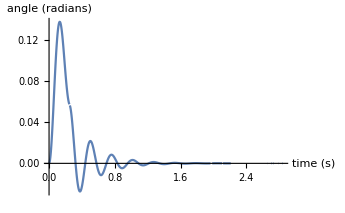

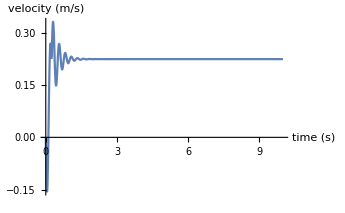

```mathematica
Subscript[θ, d][t]=(UnitStep[t]-UnitStep[t-1/4])/15;
thetaResponse =InverseLaplaceTransform[Subscript[G, fullsystemsubbed] LaplaceTransform[Subscript[θ, d][t],t,s],s,t];
vResponse =InverseLaplaceTransform[Subscript[G, fullsystemsubbed] LaplaceTransform[Subscript[θ, d][t],t,s]/(Subscript[G, VELOCITYTOANGLE]/.parameters),s,t];
Plot[thetaResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "angle (radians)"}]
Plot[vResponse,{t,0,10},PlotRange-> All,AxesLabel->{"time (s)", "velocity (m/s)"}]
```